## Continuity Implies Uniform Continuity

## Of course this only applies on a closed interval

Theorem 1 on p. 143 is kind of a shock: If f is continuous on [a,b] then f is uniformly continuous on [a,b].

Couldn’t the function get steeper and steeper?

Consider the function f[x]=√(|x|)

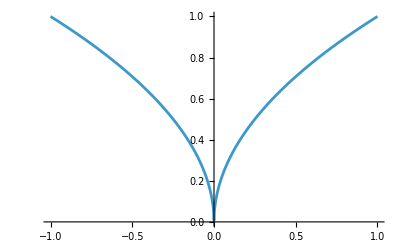

```mathematica
Plot[Sqrt[Abs[x]],{x,-1,1},PlotRange->{{-1,1},{0,1}},PlotPoints->1000]
```

This function gets arbitrarily steep near 0. Therefore an ϵ that works for a given δ near say x=1/2 isn’t going to work at x=1/4 or x=1/8 because at some point, that δ is just not small enough.

Isn’t this a counter-example to Theorem 1 on p. 143?

The answer is no or it wouldn’t be a theorem. For definiteness, consider the interval [0,1].

The trick is to go straight to the worst point, where the function is steepest, which is at x=0. Whatever δ works there works at all the places where the function is less steep.

The δ that works there, we already have found in prior problem sets, it is δ=ϵ^2.